```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

## Initialize orbit 1607 J-V, J_E-V data The diff is that we average by 4 this time

### pot offset (in V)?

```mathematica
potTFactor=0;
```

### And the data ...

```mathematica
time={"07:06:46.192","07:06:47.453","07:06:48.713","07:06:49.974","07:06:51.235","07:06:52.496","07:06:53.757","07:06:55.018","07:06:56.279","07:06:57.540","07:06:58.801","07:07:00.061","07:07:01.322","07:07:02.583","07:07:03.844","07:07:05.105","07:07:06.366","07:07:07.627","07:07:08.888","07:07:10.149","07:07:11.409","07:07:12.670","07:07:13.931","07:07:15.192","07:07:16.453","07:07:17.714","07:07:18.975","07:07:20.236","07:07:21.497","07:07:22.757","07:07:24.018","07:07:25.279","07:07:26.540","07:07:27.801","07:07:29.062","07:07:30.323","07:07:31.584","07:07:32.845","07:07:34.105","07:07:35.366","07:07:36.627","07:07:37.888","07:07:39.149","07:07:40.410","07:07:41.671","07:07:42.932","07:07:44.192","07:07:45.453","07:07:46.714","07:07:47.975","07:07:49.236","07:07:50.497","07:07:51.758","07:07:53.019","07:07:54.279","07:07:55.540","07:07:56.801","07:07:58.062","07:07:59.323","07:08:00.584","07:08:01.845","07:08:03.106","07:08:04.367","07:08:05.627","07:08:06.888","07:08:08.149","07:08:09.410","07:08:10.671","07:08:11.932","07:08:13.193","07:08:14.454","07:08:15.714","07:08:16.975","07:08:18.236","07:08:19.497","07:08:20.758","07:08:22.019","07:08:23.280","07:08:24.541","07:08:25.801","07:08:27.062","07:08:28.323","07:08:29.584","07:08:30.845","07:08:32.106","07:08:33.367","07:08:34.628","07:08:35.888","07:08:37.149","07:08:38.410","07:08:39.671","07:08:40.932","07:08:42.193","07:08:43.454","07:08:44.714","07:08:45.975","07:08:47.236","07:08:48.497","07:08:49.758","07:08:51.019","07:08:52.280","07:08:53.541","07:08:54.801","07:08:56.062","07:08:57.323","07:08:58.584","07:08:59.845","07:09:01.106","07:09:02.367","07:09:03.628","07:09:04.888","07:09:06.149","07:09:07.410","07:09:08.671","07:09:09.932","07:09:11.193","07:09:12.454","07:09:13.714","07:09:14.975","07:09:16.236","07:09:17.497","07:09:18.758","07:09:20.019","07:09:21.280","07:09:22.541","07:09:23.801","07:09:25.062","07:09:26.323","07:09:27.584","07:09:28.845"};
pots={815.36,815.36,940.80,940.80,940.80,564.48,407.68,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,689.92,689.92,689.92,689.92,689.92,689.92,689.92,564.48,564.48,564.48,407.68,689.92,344.96,344.96,344.96,1379.84,344.96,1379.84,1128.96,1128.96,1128.96,344.96,1128.96,1128.96,1128.96,1128.96,1128.96,1379.84,1379.84,1379.84,1630.72,1881.60,2257.92,3763.20,3763.20,3261.44,3261.44,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.20,4515.84,3763.20,4515.84,3763.20,3763.20,3763.20,3763.20,3261.44,3763.20,3261.44,2759.68,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,1881.60,1881.60,1881.60,1881.60,1379.84,1128.96,940.80,940.80,815.36,940.80,940.80,1379.84,1379.84,1630.72,1881.60,1881.60,1881.60,2257.92,2257.92,2257.92,1630.72,1630.72,1630.72,1379.84,1379.84,1128.96,940.80,1128.96,815.36,689.92,564.48,470.40,344.96,344.96,344.96,344.96,344.96,344.96,344.96,407.68,344.96,407.68,344.96,344.96,344.96};
curs={1.114,1.148,1.425,1.573,1.572,1.097,0.522,0.147,0.140,0.233,0.166,0.163,0.140,0.184,0.581,0.727,0.976,1.262,1.302,1.144,1.245,1.340,1.080,1.153,0.924,0.575,0.887,1.527,2.018,1.863,1.706,1.631,1.189,1.043,0.980,0.954,1.103,0.985,1.306,1.331,1.478,1.383,1.383,1.378,1.875,3.082,3.482,4.108,3.946,4.078,3.352,3.998,4.592,4.795,4.257,4.048,3.889,3.995,3.839,3.478,3.146,3.277,3.402,3.292,3.505,3.389,3.150,3.059,3.264,3.522,3.352,2.971,2.610,2.809,2.753,3.236,3.285,2.586,1.738,1.728,1.553,1.739,1.935,2.217,2.045,1.732,1.698,1.949,1.998,1.821,1.668,1.469,1.229,1.116,1.326,1.345,1.486,1.506,1.722,1.896,1.998,2.069,2.052,1.684,1.447,1.260,1.501,1.311,1.568,1.594,1.898,1.682,1.041,0.885,0.811,0.793,0.575,0.453,0.362,0.358,0.337,0.333,0.372,0.347,0.372,0.399,0.406,0.396,0.414,0.408};
curErrs={0.045,0.099,0.111,0.141,0.084,0.110,0.092,0.040,0.086,0.117,0.053,0.063,0.053,0.162,0.067,0.128,0.075,0.047,0.050,0.046,0.045,0.065,0.053,0.052,0.041,0.346,0.479,0.236,0.131,0.040,0.037,0.037,0.028,0.028,0.026,0.025,0.023,0.030,0.030,0.033,0.031,0.041,0.037,0.038,0.039,0.066,0.070,0.087,0.067,0.100,0.079,0.090,0.086,0.117,0.113,0.117,0.086,0.122,0.100,0.117,0.086,0.095,0.092,0.099,0.079,0.143,0.122,0.156,0.098,0.176,0.161,0.169,0.119,0.181,0.163,0.232,0.142,0.249,0.174,0.163,0.113,0.299,0.349,0.321,0.156,0.596,0.602,0.939,0.198,0.069,0.066,0.065,0.043,0.057,0.067,0.067,0.063,0.036,0.037,0.037,0.036,0.043,0.040,0.038,0.031,0.036,0.040,0.034,0.037,0.047,0.047,0.042,0.032,0.033,0.033,0.030,0.026,0.042,0.032,0.033,0.029,0.029,0.030,0.027,0.025,0.044,0.041,0.037,0.037,0.043};
jes={1.259,1.270,1.796,1.862,1.540,0.816,0.398,0.171,0.179,0.244,0.230,0.246,0.209,0.244,0.513,0.693,0.884,1.168,1.237,1.108,1.184,1.230,0.988,1.051,0.821,0.528,0.868,1.644,2.221,2.204,2.339,2.184,1.687,1.442,1.373,1.345,1.505,1.339,1.622,1.709,1.940,1.812,2.055,2.041,2.794,4.978,6.532,9.688,12.215,14.021,10.622,13.317,17.971,18.587,16.854,16.331,16.130,16.244,15.905,14.905,12.987,13.189,14.129,13.888,14.345,13.307,12.089,12.092,12.649,13.627,12.517,11.282,9.824,9.807,9.272,11.564,11.117,7.545,4.573,4.303,3.933,4.464,5.049,5.799,5.193,3.890,3.741,4.361,4.104,3.198,2.627,2.285,1.904,1.689,2.111,2.337,2.737,2.910,3.570,4.324,4.809,5.020,5.136,4.393,3.537,2.991,3.041,2.646,3.304,2.784,3.245,3.004,2.530,2.242,2.048,1.678,1.487,1.191,1.010,1.119,1.107,1.107,1.367,1.269,1.462,1.525,1.556,1.485,1.622,1.691};
jeErrs={0.250,0.545,0.527,0.607,0.334,4.853,0.228,0.175,0.150,0.183,0.153,0.211,0.253,1.988,1.516,0.492,0.277,0.237,0.209,0.200,0.183,0.234,0.174,0.195,0.168,3.451,2.002,2.461,10.706,0.172,0.174,0.155,0.139,0.149,0.134,0.122,0.113,0.157,0.154,0.173,0.163,0.216,0.200,0.210,0.237,0.409,0.454,0.642,0.584,0.949,0.730,0.927,0.981,1.132,1.125,1.208,1.029,1.437,1.095,1.312,1.011,1.172,1.018,1.161,1.026,1.688,1.213,1.558,1.125,1.990,1.564,1.635,1.281,1.998,1.358,2.038,1.522,2.979,1.796,1.299,1.001,3.004,38.048,2.560,1.339,4.541,7.903,18.922,2.022,0.485,0.386,0.392,0.271,0.307,0.359,0.423,0.508,0.244,0.273,0.299,0.336,0.366,0.351,0.331,0.260,0.301,0.272,0.251,0.294,0.273,0.285,0.286,0.282,0.227,0.202,0.179,0.159,0.196,0.190,0.270,0.191,0.215,0.205,0.214,0.236,0.373,0.359,0.239,0.347,0.423};
```

## Manip plots to decide on indices to use

### Check out J-V relation

```mathematica
ind1Start=0;ind1End=45;ind1Init=45;ind2Init=53;(*Jim alt?*)
```

```mathematica
ind1Start=0;ind1End=100;ind1Init=67;ind2Init=117;(*Jim alt?*)
```

```mathematica
ind1Start=0;ind1End=100;ind1Init=91;ind2Init=117;(*Jim alt?*)
```

```mathematica
ind1Start=0;ind1End=100;ind1Init=65;ind2Init=118;(*Jim alt?*)
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],AxesStyle->(FontSize->24),PlotRange->{{000,Max[pots]*1.1},{0,Max[curs]*1.1}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

### Check out energy flux–voltage relation

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,Max[pots]},{0,Max[jes]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

The fits—J-V, J_E-V, and combined

## Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
inds1=Range[65,118];
```

```mathematica
inds2=Range[90,107]; (*Super-low kappa*)
```

```mathematica
inds3={3,4}~Join~inds2;
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorJe1,errorJe2,errorJe3}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

## Fits: Select indices to use, setup bounds and initial guesses

### Which to use?

```mathematica
useinds1=1; (*Else use inds2*)
```

### Bounds

```mathematica
minFitT=20;
maxFitT=5000;
minFitRB=3;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
```

#### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds1 ...

## Nonlinear J-V fits

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,10<kFitT<4000,3<kFitRB<1000000,1.501<kFitKappa<20};
gConstraints={0.01<gFitN<10,10<gFitT<4000,3<gFitRB<1000000};*)
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[jData,{kModel,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts];
```

```mathematica
gFit=NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
```

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
```

## Nonlinear J_E-V fits

### Initial guesses

```mathematica
(*kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;*)
```

```mathematica
(*gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;*)
```

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};*)
```

```mathematica
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFitJeV=NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts];
```

```mathematica
gFitJeV=NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
```

```mathematica
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
```

## Now J-V and J_E-V fits simultaneously!

```mathematica
(*RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;*)
```

```mathematica
(*RBinit=kBestJeVRB;Tminit=kBestJeVT;nminit=kBestJeVN;kappainit=kBestJeVKappa;*)
```

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];
```

```mathematica
gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts];
```

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts];
```

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
```

```mathematica
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};
```

Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=4000;
```

```mathematica
minJ=0;maxJ=4;
```

```mathematica
minJe=0;maxJe=12.;
```

### Setup combined fit plots

```mathematica
parNames={"T_m : ","n_m : ","R_B : ","χ_red^2:"};
vSpace=0.5;
pTableFontSize=16;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJVVals~Join~{""}~Join~kJVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJeVVals~Join~{""}~Join~kJeVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gCombVals~Join~{""}~Join~kCombVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[{0.12,0.7}]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref="Orb1607";
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
```

```mathematica
(*combJVPref="combJVJeVFit__JV";
combJeVPref="combJVJeVFit__JeV";*)
```

```mathematica
(*{JVFilename,JeVFilename,combJVFilename,combJeVFilename}=(ToString@StringForm["`1`__`2`__inds_`3`-`4`.png",orbPref,#,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combJVPref,combJeVPref}*)
```

```mathematica
If[potTFactor == 0,suffString="",suffString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

```mathematica
{JVFilename,JeVFilename,combFilename}=(ToString@StringForm["`1`__`2``3`__inds_`4`-`5`.png",orbPref,#,suffString,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combPref}
```

{Orb1607__JVFit__inds_65-118.png,Orb1607__JeVFit__inds_65-118.png,Orb1607__combJVJeVFit__inds_65-118.png}

### J-V plot

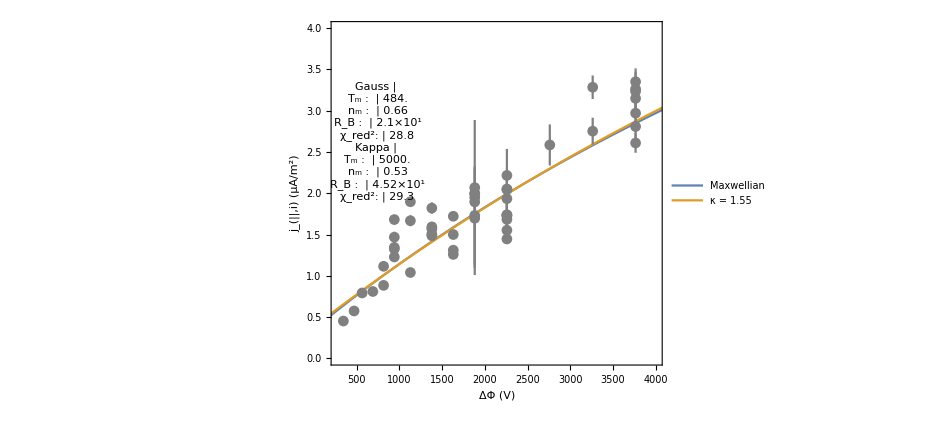

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

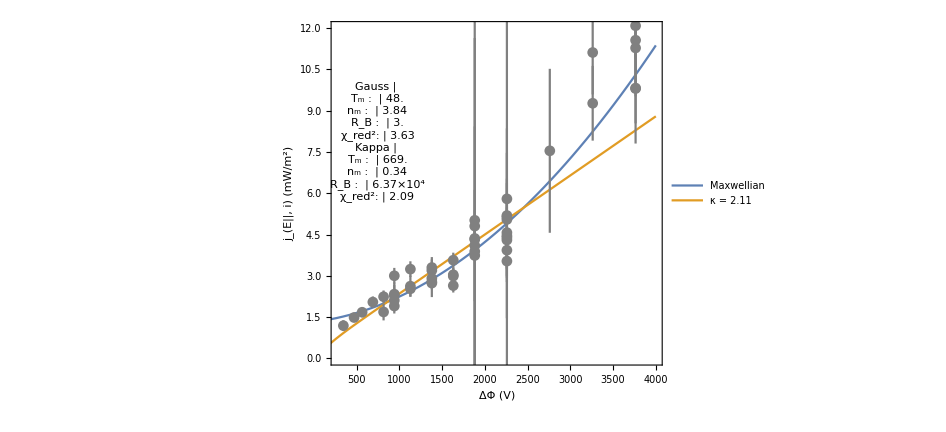

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,4000},PlotRange->{{minPot,maxPot},{minJe,maxJe}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

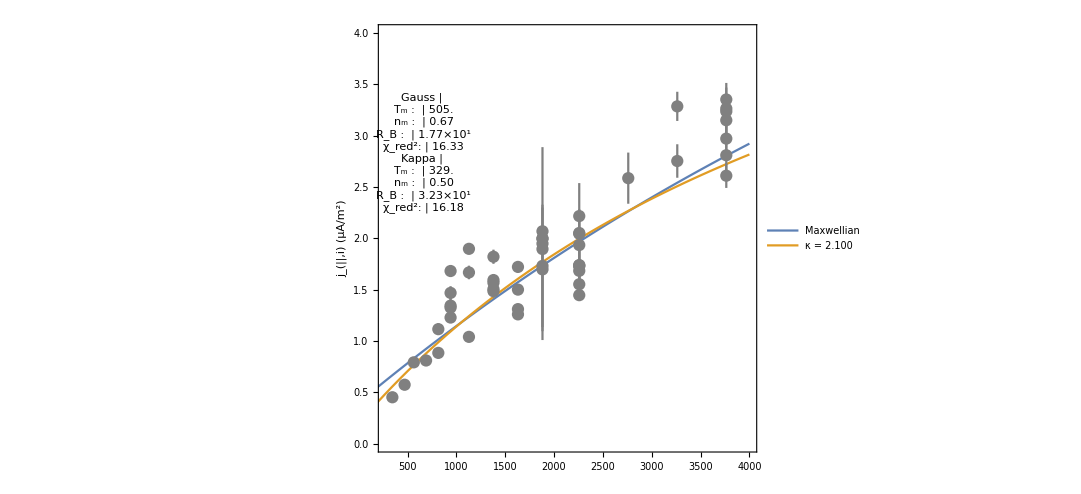
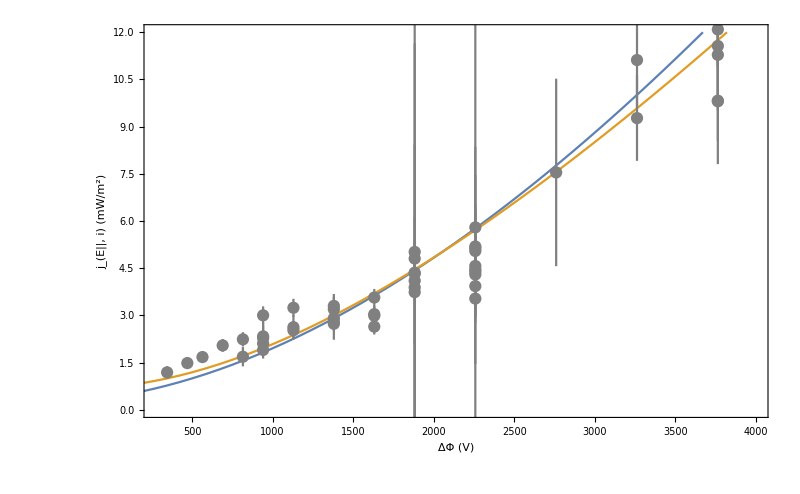

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

```mathematica
makePlots=1;
```

```mathematica
(*If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Export[dir<>JeVFilename,JeVPlot];Export[dir<>combJVFilename,combJVPlot];Export[dir<>combJeVFilename,combJeVPlot];Print["Done!"]]*)
```

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180316/ ...

Orb1607__JeVFit__inds_65-97.png ...

Orb1607__combJVJeVFit__inds_65-97.png ...

Done!

Param tables

### J-V params

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.0788489 | 18.0635 | 0.0043651 | 0.996563
kFitT | 20.0084 | 211292. | 0.0000946954 | 0.999925
kFitRB | 999996. | 413.953 | 2415.72 | 1.33998×10^-53
kFitKappa | 1.5077 | 82.2571 | 0.0183292 | 0.985567

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.737783 | 2.50754 | 0.294226 | 0.771617
gFitT | 20. | 189.449 | 0.10557 | 0.916976
gFitRB | 336621. | 1.19817×10^10 | 0.0000280946 | 0.999978

### J_E-V params

```mathematica
kFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.590468 | 12.8417 | 0.0459806 | 0.963806
kFitT | 20.0001 | 209.717 | 0.0953669 | 0.925022
kFitRB | 239189. | 4.5854×10^9 | 0.0000521631 | 0.999959
kFitKappa | 2.43713 | 84.7723 | 0.0287491 | 0.977365

```mathematica
gFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.762078 | 0.387809 | 1.96508 | 0.063448
gFitT | 20. | 47.5033 | 0.421023 | 0.678228
gFitRB | 330538. | 6.09865×10^9 | 0.0000541986 | 0.999957

### Params from combined fit

```mathematica
kCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitRB | 805633. | 8.95543×10^9 | 0.0000899603 | 0.999929
kFitT | 20. | 157.058 | 0.127342 | 0.899278
kFitN | 0.491447 | 1.8178 | 0.270352 | 0.788213
kFitKappa | 2.0396 | 0.791263 | 2.57765 | 0.0135471

```mathematica
gCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitRB | 450860. | 4.64319×10^9 | 0.0000971014 | 0.999923
gFitT | 20. | 30.7434 | 0.650545 | 0.518801
gFitN | 0.738934 | 0.408339 | 1.80961 | 0.0773503

Linear model, if we ever cared

```mathematica
jData[[;;,1]]
```

{4515.84,4515.84,3763.2,4515.84,3763.2,4515.84,3763.2,3763.2,3763.2,3763.2,3261.44,3763.2,3261.44,2759.68,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,1881.6,1881.6,1881.6,1881.6,1379.84,1128.96,940.8,940.8,815.36,940.8,940.8,1379.84,1379.84,1630.72,1881.6,1881.6,1881.6,2257.92,2257.92,2257.92,1630.72,1630.72,1630.72,1379.84,1379.84,1128.96,940.8,1128.96,815.36,689.92,564.48,470.4,344.96}

```mathematica
jData[[;;,1]]/kCombT
```

{13.7193,13.7193,11.4327,13.7193,11.4327,13.7193,11.4327,11.4327,11.4327,11.4327,9.90835,11.4327,9.90835,8.38399,6.85963,6.85963,6.85963,6.85963,6.85963,6.85963,6.85963,5.71636,5.71636,5.71636,5.71636,4.192,3.42981,2.85818,2.85818,2.47709,2.85818,2.85818,4.192,4.192,4.95418,5.71636,5.71636,5.71636,6.85963,6.85963,6.85963,4.95418,4.95418,4.95418,4.192,4.192,3.42981,2.85818,3.42981,2.47709,2.096,1.71491,1.42909,1.048}

```mathematica
Plot[jData[[;;,1]],LKKappaDensFac[jData[[;;,1]]/kCombT,kCombRB,kCombKappa]]
```

Plot::pllim: Range specification {1.55096,1.55096,1.56622,1.55096,1.56622,1.55096,1.56622,1.56622,1.56622,1.56622,1.56805,1.56622,1.56805,1.55931,1.53453,1.53453,1.53453,«18»,1.5002,1.5002,1.5002,1.53453,1.53453,1.53453,1.46669,1.46669,1.46669,1.4217,1.4217,1.36144,1.30287,1.36144,1.25556,«4»} is not of the form {x, xmin, xmax}.

Plot[jData⟦1;;All,1⟧,LKKappaDensFac[jData⟦1;;All,1⟧/kCombT,kCombRB,kCombKappa]]